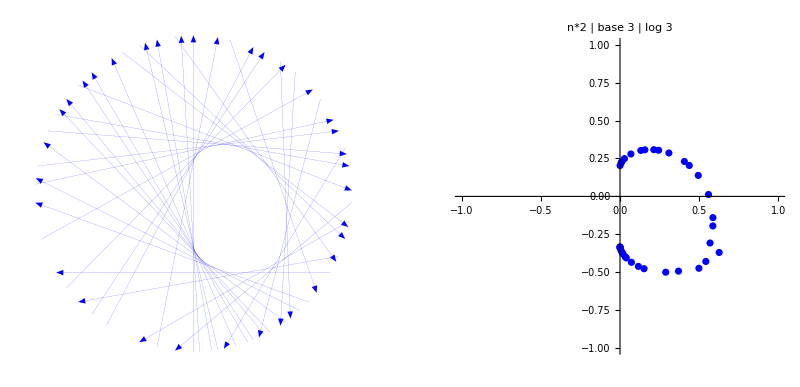

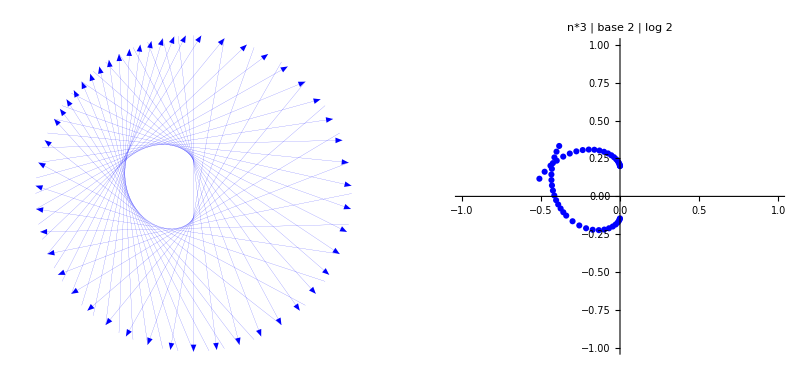

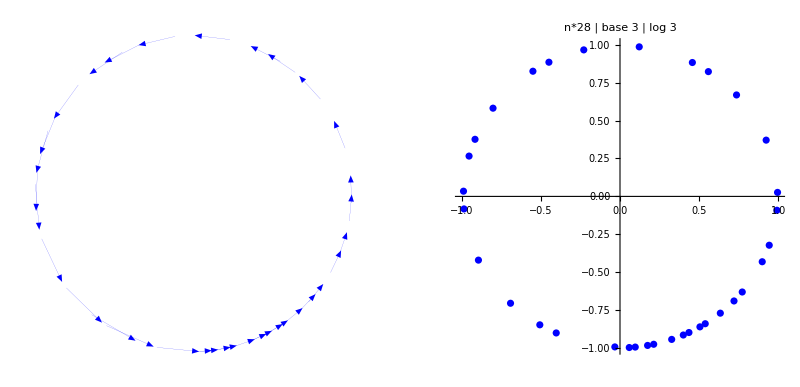

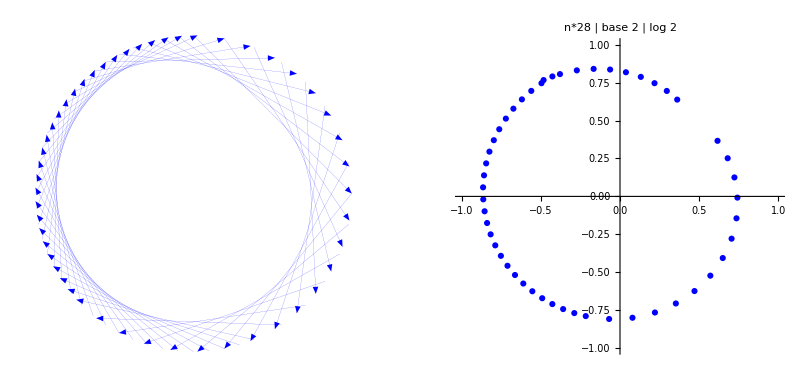

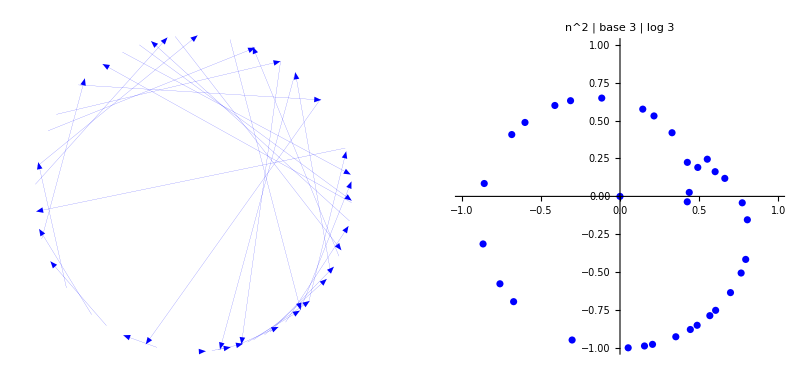

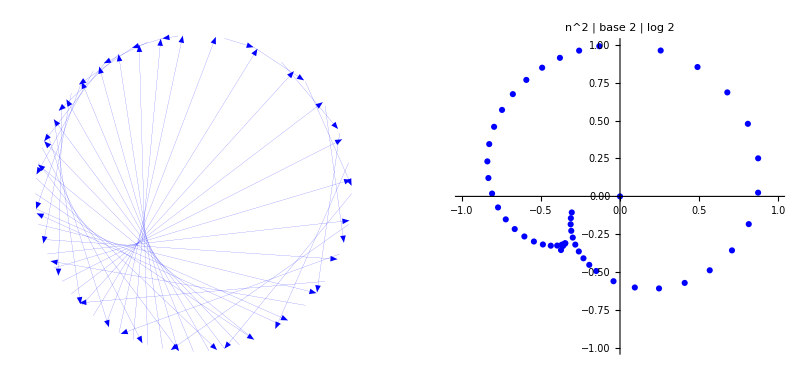

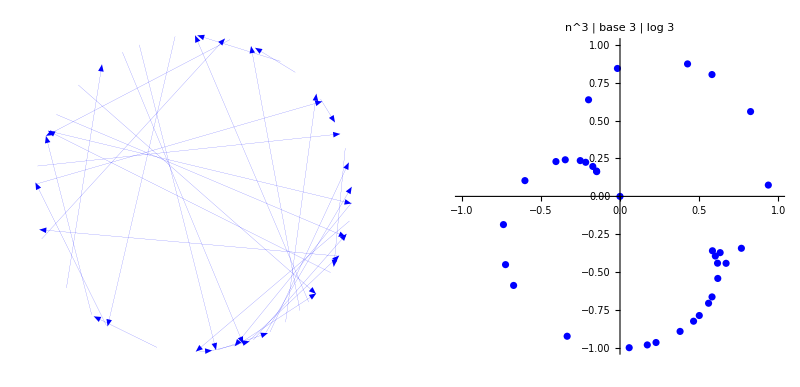

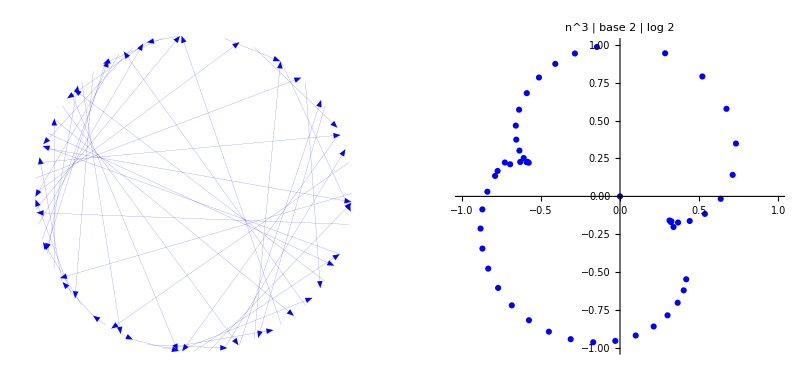

```mathematica
ClearAll["Global`*"];

angle[n_, fnfact_]:=(2*Pi*fnfact[n]);

rotate[alpha_]:=(x=-Sin[alpha];y=Cos[alpha];{x,y});

intersectLines[line1_,line2_]:=(
a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];detx=Det[{{a12,det1},{a22,det2}}];dety=Det[{{det1,a11},{det2,a21}}];det=Det[{{a11,a12},{a21,a22}}];If[det>0,{detx/det,dety/det},{0,0}]);

generatePlot[fnline_,fnfact_, step_, label_]:= (
start=1;
stop=100;
e=0.001;
(*angles1=Table[{angle[n, fnfact],angle[fnline[n], fnfact]},{n,start,stop,step}];
lines1=Map[Function[{angle1, angle2},{rotate[angle1], rotate[angle2]}], angles1];*)
lines1=Table[{rotate[angle[n, fnfact]],rotate[angle[fnline[n], fnfact]]},{n,start,stop,step}];
lines2=Table[{rotate[angle[n+e, fnfact]],rotate[angle[fnline[n+e], fnfact]]},{n,start,stop,step}];
plot1=Graphics[{Blue, Thickness[0.0001],Map[Arrow,lines1],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label}];
plot2=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label,PlotStyle->Blue];
GraphicsGrid[{{plot1,plot2}}]
);

fnline[n_]:=n*2;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
generatePlot[fnline, fnfact,3, "n*2 | base 3 | log 3"]

fnline[n_]:=n*3;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,2, "n*3 | base 2 | log 2"]

fnline[n_]:=n*28;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
generatePlot[fnline, fnfact,3, "n*28 | base 3 | log 3"]

fnline[n_]:=n*28;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,2, "n*28 | base 2 | log 2"]

fnline[n_]:=n^2;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
generatePlot[fnline, fnfact,3, "n^2 | base 3 | log 3"]

fnline[n_]:=n^2;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,2, "n^2 | base 2 | log 2"]

fnline[n_]:=n^3;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
generatePlot[fnline, fnfact,3, "n^3 | base 3 | log 3"]

fnline[n_]:=n^3;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,2, "n^3 | base 2 | log 2"]

fnline[n_]:=n*11;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
generatePlot[fnline, fnfact,3, "n*11 | base 3 | log 3"]

fnline[n_]:=n*11;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,2, "n*11 | base 2 | log 2"]

fnline[n_]:=n*4;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
generatePlot[fnline, fnfact,3, "n*4 | base 3 | log 3"]

fnline[n_]:=n*4;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,2, "n*4 | base 2 | log 2"]

fnline[n_]:=n*3;
fnfact[n_]:=n/(7^(Floor[Log[7,n]]+1)-7^Floor[Log[7,n]]);
generatePlot[fnline, fnfact,2, "n*3 | base 7 | log 7"]

fnline[n_]:=n*7;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
generatePlot[fnline, fnfact,2, "n*7 | base 3 | log 3"]

fnline[n_]:=n*5;
fnfact[n_]:=n/(11^(Floor[Log[11,n]]+1)-11^Floor[Log[11,n]]);
generatePlot[fnline, fnfact,2, "n*5 | base 11 | log 11"]

fnline[n_]:=n*11;
fnfact[n_]:=n/(5^(Floor[Log[5,n]]+1)-5^Floor[Log[5,n]]);
generatePlot[fnline, fnfact,2, "n*11 | base 5 | log 5"]
```